## Lesson 21: Laplace transform

## Overview

The techniques for solving differential equations you have learned thus far have proven to be extensively capable yet rather awkward to utilize.

A more straightforward method of solving differential equations exists based on the Laplace transform.

The Laplace transform possesses a multitude of useful properties that can be very applicable to solving differential equations.

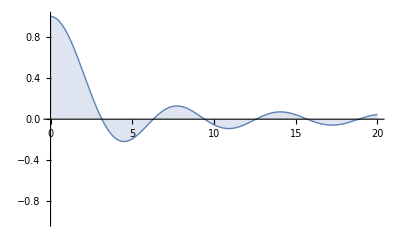

```mathematica
Plot[Sin[x]/x,{x,0,20},]
```

## Improper Integral

Because the Laplace transform involves an improper integral, the lesson begins with a brief review of improper integration.

Recall that an improper integral over an unbounded interval is defined as a limit of integrals over finite intervals:

∫_a^∞ f(t)ⅆt=lim_(A→∞) ∫_a^A f(t)ⅆt

If the limit as A→∞ exists, then the improper integral is said to converge to that limit:

```mathematica
Manipulate[Show[Plot[Sin[x]/x,{x,0,20},],Plot[Sin[x]/x,{x,0,a},],Graphics[Text[NIntegrate[Sin[x]/x,{x,0,a}],{10,.5}]]],{a,1,20}]
```

## Example of an Improper Integral

Let f(t)=e^-t. Calculate the following improper integral:

∫_0^∞ f(t)ⅆt

This can be done by first evaluating the integral over a finite interval, say [0,A].

The Wolfram Language can integrate this function for any value of A:

```mathematica
sln=Integrate[ Exp[-t],{t,0,A}]
```

1-Cosh[A]+Sinh[A]

Now you can compute the Limit to find the value of this improper integral:

```mathematica
Limit[sln, A->∞]
```

1

In fact, the Wolfram Language can directly evaluate improper integrals by setting ∞ as the upper limit in the Integrate function:

```mathematica
Integrate[ Exp[-t],{t,0,∞}]
```

1

## Example of an Improper Integral

Let f(t)=1/t. Calculate the following improper integral:

∫_1^∞ f(t)ⅆt

This can be done by first evaluating the integral over a finite interval, say from [1,A]:

```mathematica
sln=Integrate[ 1/t,{t,1,A},Assumptions->A>1]
```

Log[A]

Now you can utilize the function Limit to find the value of this improper integral:

```mathematica
Limit[sln, A->∞]
```

∞

This is an example of an improper integral that does not exist:

```mathematica
Integrate[ 1/t,{t,1,∞}]
```

Integrate::idiv: Integral of 1/t does not converge on {1,∞}.

∫_1^∞ 1/t ⅆt

This output agrees with the result obtained through manual calculations.

## Integral Transforms

The Laplace transform is one of many types of integral transforms.

Integral transforms take one function of some variable f(t) and transform this function into another function of a different variable F(s).

This transformation is performed by integrating the product of the original function f(t) and a kernel function K(s,t):

F(s)=∫_α^β K(s,t)f(t)ⅆt

Different integral transforms can have different kernel functions.

## The Laplace Transform

For the Laplace transform, the kernel takes the form e^(-s t).

The Laplace transform of a function f(t) is denoted by L{f(t)} and is defined by the equation:

L{f(t)}=F(s)=∫_0^∞ e^(-s t)f(t)ⅆt

As you will find, the Laplace transform can reduce initial value problems into quite simple forms.

Before taking the Laplace transforms into the theory of differential equations, you will begin by experimenting and discovering the techniques of evaluating these transformations.

## Example 1

Let f(t)=1. Calculate the Laplace transform of this function.

First, evaluate the improper integral:

L{1}=F(s)=∫_0^∞ e^(-s t)1ⅆt

This improper integral can be evaluated using Integrate:

```mathematica
Integrate[ Exp[-s t]*1,{t,0,∞}]
```

ConditionalExpression[1/s, Re[s]>0]

The result of the calculation shows that the Laplace transform of f(t)=1,is F(s)=1/s:

```mathematica
LaplaceTransform[1,t,s]
```

1/s

Observe that this can only be defined for s>0:

```mathematica
Integrate[ Exp[-s t]*1,{t,0,∞},Assumptions->s≤ 0]
```

Integrate::idiv: Integral of ⅇ^(-s t) does not converge on {0,∞}.

Integrate[ⅇ^(-s t),{t,0,∞},Assumptions→s≤0]

## Example 2

Let a be some constant and f(t)=e^(a t). Calculate the Laplace transform of this function.

You must evaluate the improper integral:

L{e^(a t)}=F(s)=∫_0^∞ e^(-s t)e^(a t)ⅆt.

Evaluate this improper integral using Integrate:

```mathematica
Integrate[ Exp[-s t] Exp[a t],{t,0,∞}]
```

ConditionalExpression[1/(-a+s), Re[a]<Re[s]]

The result of the calculation shows that the Laplace transform of f(t)=e^(a t), is F(s)=1/(s-a):

```mathematica
LaplaceTransform[Exp[a t],t,s]
```

1/(-a+s)

Observe that this can only be defined for s>a:

```mathematica
Integrate[ Exp[-s t] Exp[a t],{t,0,∞},Assumptions->s≤  a]
```

Integrate::idiv: Integral of ⅇ^((a-s) t) does not converge on {0,∞}.

Integrate[ⅇ^(a t-s t),{t,0,∞},Assumptions→s≤a]

## Piecewise Continuous Functions

For the Laplace transform of a function to exist, it is first necessary that the function be piecewise continuous.

A function is said to be piecewise continuous on an interval if that interval can be partitioned into finitely many subintervals where the function is continuous on each of those subintervals.

The following function is an example of a piecewise continuous function:

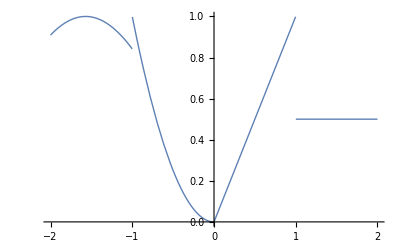

```mathematica
Plot[Piecewise[{{-Sin[x],x<-1},{x^2,-1<x<0},{x,1>x>0},{.5,x>1}}],{x,-2,2},PlotStyle->Thick]
```

## Exponential Order

The second property for the Laplace transform of a function to exist is that it must not diverge faster than an exponential function.

A function is said to possess the property of exponential order if |f(t)|≤K e^(a t) when t>M where K, M and a are real constants.

The following function is an example of a function of exponential order:

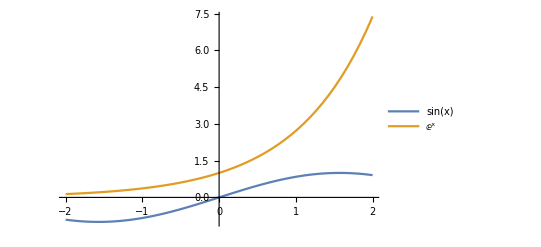

```mathematica
Plot[{Sin[x],E^x},{x,-2,2},]
```

## Example 3

Let f(t)=1 for 0≤t<1 and 0 elsewhere. Calculate the Laplace transform of this function.

You must evaluate the improper integral:

L{f(t)}=F(s)=∫_0^1 e^(-s t)1ⅆt

Evaluate this improper integral using Integrate:

```mathematica
f[t_]:=Piecewise[{{1,0≤t<1},{0,t<0},{0,t≥1}}]
```

```mathematica
Integrate[Exp[-s t] f[t],{t,0,∞}]
```

(ⅇ^-s (-1+ⅇ^s))/s

The result of the calculation shows that the Laplace transform of f(t) is  F(s)=(ⅇ^-s (-1+ⅇ^s))/s:

```mathematica
LaplaceTransform[f[t],t,s]//TrigToExp
```

1/s-ⅇ^-s/s

## Summary

This lesson explored an integral transform known as the Laplace transform:

L{f(t)}=F(s)=∫_0^∞ e^(-s t)f(t)ⅆt

It begins with one function f(t) and transforms it into a new function F(s).

You studied the necessary properties a function must possess so that the Laplace transform exists.

The role that this transformation plays will be revealed in the subsequent lessons in this chapter.